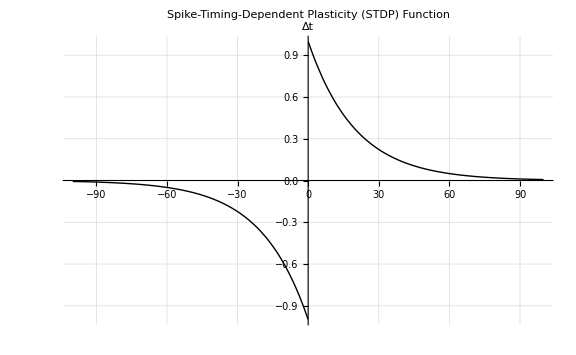

```mathematica
STDP[deltaT_]:=Piecewise[{{Aplus*Exp[-deltaT/tauplus],deltaT>0},{-Aminus*Exp[deltaT/tauminus],deltaT<0}}]



APlus=1.0;
AMinus=1.0;
tauPlus=20;
tauMinus=20;

Plot[STDP[deltaT],{deltaT,-100,100},
    PlotRange->All,
    PlotLabel->Style["Spike-Timing-Dependent Plasticity (STDP) Function",FontSize->16],
    AxesLabel->Style["Δt","W(ΔWt)", FontSize->16],
    GridLines->Automatic,
    PlotStyle->{Thick,GrayLevel[0]},
    ImageSize->Large]
```